# A Computational Method to Predict X-ray Diffraction (XRD) Patterns

Hamza Alsamraee

Mentor: Eryn Gillam

## Description

XRD has been instrumental to the advancement of many fields in both science and technology. Each distinct lattice structure has its own XRD fingerprint, which scientists use to determine the chemical makeup of the lattice and in turn its physical properties. In this project, a large mathematical framework was utilized to effectively predict XRD patterns produced by various cubic lattice structures.  First, the Bragg peak positions were computed from Bragg’s law with high accuracy. Structure factor was also computed for both unary and binary systems and used to compute intensity alongside plane multiplicity. High accuracy was found for unary systems, but binary systems showed less accurate predictions.

## Getting the Bragg Peak Positions

#### Some Data

Importing the lattice constant and structure data

```mathematica
rawdata=Import["C:\\Users\\hamza\\Desktop\\project\\lattice data.xlsx", "Data"];
```

Establishing column names and deleting extraneous columns

```mathematica
latticeAssoc=Function[u,<|"Compound"-> u⟦1⟧,"LatticeConstant"->ToExpression[u⟦2⟧],"Structure"-> u⟦3⟧|>]/@First[rawdata]⟦All,1;;3⟧;
```

Making a dataset

```mathematica
latticeDataset=Dataset[latticeAssoc]
```

Dataset[<>]

“toCompound” converts a cation/anion pair to a compound, so it is compatible with the above dataset. It takes off the last two characters (indicating charge) and joins cation/anion to make the name of a compound

```mathematica
toCompound[list_] := StringJoin[StringDrop[#,-2] & /@ list]
```

#### Bragg’s Law

Given a d spacing value and a wavelength, this function gives back the Bragg peak positions

```mathematica
theta[d_,w_] := 2 ArcSin[(w/( 2  d))  ]
```

#### Allowed Reflections

For different structures, certain planes have no contribution to peak intensity. For a body centered cubic unit cell, the total of h+k+l (Miller indices) has to be even to have a nonzero structure factor. For a face centered cubic unit cell, the parity of the Miller indices has to all be the same. To test for the same parity, an EvenQ function was mapped to the list of Miller indices; if they are all the same parity, there will be only one list element after deleting duplicates.

```mathematica
reflections[list_,n_]:= Drop[If[Length @ list==1,(If[ElementData[First @ list,"CrystalStructure"]["Name"]=="body-centered cubic" , Select[Flatten[Table[{h,k,l} ,{h,0,n},{k,0,n},{l,0,n}],2],EvenQ[Total[#]]&], If[ElementData[First @ list,"CrystalStructure"]["Name"]=="face-centered cubic",Select[Flatten[Table[{h,k,l} ,{h,0,n},{k,0,n},{l,0,n}],2],Length @ DeleteDuplicates[EvenQ/@ #] ==1&],{}],{}]), If[Length @ list==2, (If[First@Normal[latticeDataset[Select[#Compound==toCompound[list]&],"Structure" ]]=="body-centered cubic" , Select[Flatten[Table[{h,k,l} ,{h,0,n},{k,0,n},{l,0,n}],2],EvenQ[Total[#]]&], If[First@Normal[latticeDataset[Select[#Compound==toCompound[list]&],"Structure" ]]=="face-centered cubic",Select[Flatten[Table[{h,k,l} ,{h,0,n},{k,0,n},{l,0,n}],2],Length @ DeleteDuplicates[EvenQ/@ #] ==1&],{}],{}]),{}],{}],1]
```

Here is an example:

```mathematica
reflections[{"Na"},2]
```

{{0,0,2},{0,1,1},{0,2,0},{0,2,2},{1,0,1},{1,1,0},{1,1,2},{1,2,1},{2,0,0},{2,0,2},{2,1,1},{2,2,0},{2,2,2}}

Now, we proceed to group Miller indices by d spacing (“a”, the lattice constant, is left out since it is consistent across all planes).

```mathematica
grouped[list_,n_]:=GroupBy[ reflections[list,n],1/Sqrt[(#[[1]]^2+#[[2]]^2+#[[3]]^2)]&]
```

Here is an example:

```mathematica
grouped[{"Li1+","Cl1-"},2]
```

<|1/2→{{0,0,2},{0,2,0},{2,0,0}},1/(2 √2)→{{0,2,2},{2,0,2},{2,2,0}},1/(√3)→{{1,1,1}},1/(2 √3)→{{2,2,2}}|>

The keys of this function are transformed from the normalized d-spacing to theta values. For unary systems, I used the Wolfram database to import the lattice constant to obtain accurate d-spacing. For binary systems, a handmade dataset was used to extract lattice constants.

```mathematica
keytransform[w_,list_,n_]:=If[ Length@ list ==1,theta[QuantityMagnitude [
UnitConvert[First @ ElementData[ElementData[First@list,"StandardName"],"LatticeConstants"],"Angstroms"]]*(grouped[list,n] //Keys),w]//N, If[ Length @ list ==2, theta[First[Normal[latticeDataset[Select[#Compound==toCompound[list]&],"LatticeConstant" ]]]*(grouped[list,n] //Keys),w]//N,{}],{}]
```

A list of associations is made so theta values and Miller indices can be called easily.

```mathematica
association[list_,n_,w_] := Sort[MapThread[#1->#2&,{keytransform[w,list,n],grouped[list,n]//Values}]]
```

Here is an example:

```mathematica
association[{"Na1+","Cl1-"},3,1.54]
```

{0.477458→{{1,1,1}},0.553123→{{0,0,2},{0,2,0},{2,0,0}},0.79291→{{0,2,2},{2,0,2},{2,2,0}},0.93981→{{1,1,3},{1,3,1},{3,1,1}},0.98524→{{2,2,2}},1.27477→{{1,3,3},{3,1,3},{3,3,1}},1.5773→{{3,3,3}}}

## Atomic Form Factors

Importing another database for values to be used for calculating the atomic form factor.

```mathematica
Import["C:\\Users\\hamza\\Desktop\\project\\Untitled spreadsheet.xlsx","Elements"]
```

{Data,Dataset,Dimensions,FormattedData,Formulas,Images,SheetCount,Sheets}

```mathematica
atomic =Import["C:\\Users\\hamza\\Desktop\\project\\Untitled spreadsheet.xlsx","Dataset"]
```

{Dataset[<>]}

Getting the Columns

```mathematica
dataset=atomic[[1]];
```

```mathematica
columns=Normal[dataset]//First
```

{Element,a1,b1,a2,b2,a3,b3,a4,b4,c}

```mathematica
data=Rest[Normal[dataset]];
```

Making a wolfram dataset

```mathematica
assocData=Association@@MapThread[Rule,{columns,#}]&/@data;
```

```mathematica
newDataset=Dataset[assocData];
```

```mathematica
newDataset
```

Dataset[<>]

F is the function that approximates the form factors as a sum of gaussians. See https://en.wikipedia.org/wiki/Atomic_form_factor

```mathematica
F[{a_,b_,c_, w_, theta_}] := (a *Exp[-b ( Sin [theta/2] /w)^2]+c )
```

Making a function to extract data. Takes the a_i and b_i values as well as c and plugs it into F to get the atomic form factors.

```mathematica
atomdata[e_,theta_,w_]:=Total[F /@ Table[{First[Normal[newDataset[Select[#Element==e[[1]] &]]]][[i]],First[Normal[newDataset[Select[#Element== e[[1]]&]]]][[i+1]], First[Normal[newDataset[Select[#Element==e[[1]]&]]]][[10]],w,theta}, {i,2,8,2}]]
sc[in_,w_]:=
Plot[atomdata[in,theta,w],{theta,0,Pi/2},AxesLabel-> {"Angle","Atomic Form Factor"}]
```

“sc” plots the atomic form factor as a function of the angle

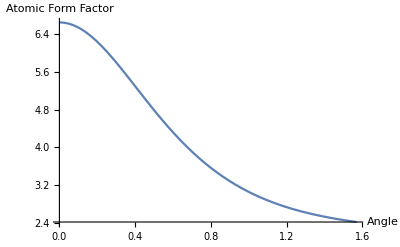

```mathematica
sc[{"C"},1.54 ]
```

Here is an example of the atomdata function:

```mathematica
atomdata[#,.8,1.54] & /@ {{"Li1+"},{"C"}}
```

{1.69118,3.56636}

## Structure Factor Calculation

For binary FCC systems, the parity of the Miller indices has to be accounted for. If the Miller indices are even, then a total of the atomic form factors is used for the structure factor. If the indices are odd, the difference is taken.

```mathematica
evenodd[b_,elementlist_,theta_,w_] := If[b,Total[atomdata[#,theta,w] & /@ elementlist], Differences[atomdata[#,theta,w] & /@ elementlist]//First]
```

The structure factor is different for each type of structure. It is given by this formula:
-Graphics-

Where f_j denotes the jth atomic form factor and (x,y,z) indicate atom position. For BCC and FCC, this formula simplifies greatly. Evenodd was used for binary systems to account for the parity of the Miller indices.

```mathematica
structurefactor[elementlist_,  w_,list_] :=
If[ 
Length@elementlist==1,If[ElementData[First@First @ elementlist,"CrystalStructure"]["Name"]=="body-centered cubic",2 *atomdata[Flatten@elementlist,#,w]& /@ (list //Keys), If[ElementData[First@First @ elementlist,"CrystalStructure"]["Name"]=="face-centered cubic" ,
4 * atomdata[Flatten@elementlist,#,w]& /@ (list //Keys) ,{}],{}],If[Length@ elementlist==2,4*
MapThread[evenodd[#1,elementlist,#2,w] & , {(EvenQ/@  First /@ First/@ (list//Values)),list//Keys}]
,{}],{}]
```

### Multiplicity

Take a look at the following graphic of planes given by Miller indices:

File:Miller Indices Felix Kling.svg. (n.d.). Retrieved from https://commons.wikimedia.org/wiki/File:Miller_Indices_Felix_Kling.svg

You might notice that if we reflect (100) we can get (010) and (001) . We can also get negative indices, usually denoted  OverBar[1]  instead of -1. This gives us 6 total planes that are symmetry-equivalent, and correspond to the same peak. Hence, we say that the class of Miller indices (h00) has a multiplicity of 6. These multiplicities range from 6 to 48 for a cubic lattice structure, but can get as low as 2 with less symmetric structures. 

Therefore, instead of calculating the contributed intensity of each plane, we count them as one plane and multiply the resultant intensity by a specific multiplicity. This multiplicity is then used to calculate peak intensity.

```mathematica
multiplicity[list_]:=
	Which[
		MemberQ[{list},{h_,h_,h_}],8,
		MemberQ[{list},{h_,0,0}],6,
		MemberQ[{list},{0,k_,0}],6,
		MemberQ[{list},{0,0,l_}],6,
		MemberQ[{list},{h_,h_,0_}],12,
		MemberQ[{list},{0_,k_,k_}],12,
		MemberQ[{list},{h_,k_,0}],24,
		MemberQ[{list},{h_,0,l_}],24,
		MemberQ[{list},{0,k_,l_}],24,
		MemberQ[{list},{h_,h_,l_}],24,	
		MemberQ[{list},{h_,k_,l_}],48]
```

Here is an example:

```mathematica
multiplicity[{1,1,1}]
```

8

## Intensity Calculation

This intensity function gives the intensity for each peak, and does so by multiplying three factors: Lorentz Polarization correction, multiplicity, and the square of the  structure factor.

```mathematica
intensity[w_,elementlist_,n_] :=Transpose@{(association[Flatten @ elementlist,n,w]//Keys),(.5(1+(Cos[#])^2)/(Sin[#/2]^2 * Cos[#/2]))& /@ (association[Flatten @ elementlist,n,w] //Keys) *
(multiplicity/@ (Last/@ (association[Flatten @ elementlist,n,w]//Values)))*(structurefactor[elementlist,w,(association[Flatten @ elementlist,n,w])]) ^2 }
```

Here is an example:

```mathematica
intensity[1.54,{{"Cu"}},2]
```

{{0.755735,509100.},{0.880166,242598.},{1.2932,147611.},{1.65984,55657.5}}

#### Getting the Final Plot

“peak” takes a set of theta values and their respective intensities, which are given by the “intensity” function. An arbitrary peak shape was chosen, and the -10000 is an arbitrary constant. If Rietveld refinement were to be used, this constant would be optimized and peak shape would change as well.

```mathematica
peak[{theta_,intensity_}] :=  intensity * Exp[-10000 Pi (t -theta)^2]
```

```mathematica
p=peak[#] & /@ intensity[1.54,{{"Ag"}},2]
```

{2.88657×10^6 ⅇ^(-10000 π (-0.665108+t)^2),1.4363×10^6 ⅇ^(-10000 π (-0.773027+t)^2),986121. ⅇ^(-10000 π (-1.12453+t)^2),362362. ⅇ^(-10000 π (-1.42286+t)^2)}

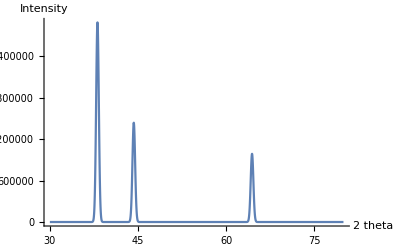

```mathematica
Quiet[Plot[Total[p]/.t->(x/90*Pi/2), {x,30,80},PlotRange->All, AxesLabel-> {"2 theta","Intensity"}]]
```

## Summary

In this project, simple mathematical models of XRD were used to predict various XRD patterns, for both unary and binary systems. For unary systems, the peaks and relative intensities were predicted with high accuracy. However, binary systems showed mediocre results, as relative intensities were often wrong. Attempts at effective prediction of lattice structure from first principles failed. Multiplicities were manually entered instead of being computed, however, crystallographic point groups showed significant promise in computing multiplicities. The crystallographic point group approach was not feasible given the two week time constraint.

## Future Work

Thanks to Mr. Wolfram, I certainly have a lot to do this summer! The eventual goal of this project is to create software with a simple UI, ie the user has to type in as little data as possible, that can predict the XRD pattern of complex inorganic lattice structures. This software would be used by scientists and industry experts alike to have reference patterns for experimental results. The first step in realizing this goal is improving accuracy for binary systems, and expanding from only cubic structures to more complex structures such as hexagonal and monoclinic lattice structures. More complicated multiatomic structures will then be implemented as well.

Perhaps the most ambitious of my future plans is doing the inverse problem: predicting the lattice structure from a given XRD pattern using machine learning. Ideally, a machine learning algorithm would be trained on a large dataset generated by the expanded XRD prediction software, and eventually be tested on the Inorganic Crystal Structure Database (ICSD).

## Acknowledgements

I would like to thank my mentor, Eryn Gillam, for helping me throughout my project. I would also like to thank the other mentors for their help, and Mohammad Bahrami for his lectures. Wolfram Summer Camp truly gave me an outlet to express my creativity in novel ways, and the two weeks I spent here were invaluable. Wolfram Summer Camp gave me a novel perspective on how to approach all aspects of life, and key insight into how computational thinking can change the world. For these reasons and more, I am beyond grateful to have been a part of this camp, and am looking forward to apply my new skills.

## References

- Miller indices pictures. Miller Indices Felix Kling.svg. (n.d.). Retrieved from WikiMedia

- Predicted vs Experimental Silver XRD Pattern. Experimental plot obtained from: Koohpeima, Fatemeh & Mokhtari, Mohammad & Samaneh, KHALAFI. (2017). The effect of silver nanoparticles on composite shear bond strength to dentin with different adhesion protocols. Journal of Applied Oral Science. 25. 367-373. 10.1590/1678-7757-2016-0391.